# Using Mathematica for Stream Plots of 2D Linear Systems of First-Order ODEs

## Problem Definition

Let’s consider the linear system of differential equations given by

```mathematica
f[x_,y_] = r x - a x y
g[x_,y_] = -k y + b x y
```

r x-a x y

-k y+b x y

```mathematica
F[x_,y_]= k Log[x] + r Log[y] - b x - a y
```

-b x-a y+k Log[x]+r Log[y]

```mathematica
paramVals = {r->1, k ->1, a->1, b ->1} (*select parameter values*)
Plot3D[
F[x,y]/.paramVals,(*Plot the curve z = F[x,y] with the parameter values*)
{x,0,4},{y,0,4},(*select range for x and y values*)
PlotPoints->100 (*increase the number of points*)
]
```

{r→1,k→1,a→1,b→1}

-Graphics3D-

```mathematica
F[4,4.]/.paramVals
```

-5.22741

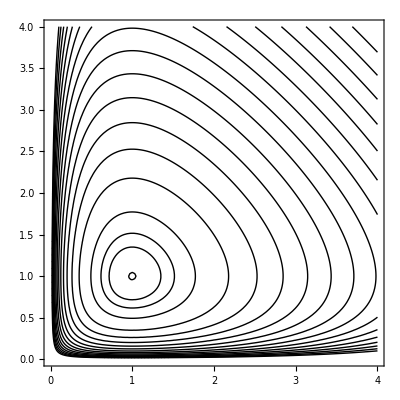

```mathematica
ContourPlot[
F[x,y]/.paramVals,(*Plot the curve z = F[x,y] with the parameter values*)
{x,0,4},{y,0,4},(*select range for x and y values*)
Contours->Flatten[{-2.001,-2.05, -2.1,Table[-2/10 i - 2.,{i,0,15}]}],
PlotPoints->50,
ContourShading->None,
ContourStyle->Thick
]
```

```mathematica
Table[-2/10 i - 2.,{i,0,10}]
```

{-2.,-2.2,-2.4,-2.6,-2.8,-3.,-3.2,-3.4,-3.6,-3.8,-4.}

```mathematica
?ContourPlot
```